```mathematica
ReflectedPowerS[n1_,n2_,θi_:0]:=Abs[(n1 Cos[θi]-n2 √(1-(n1/n2 Sin[θi])^2))/(n1 Cos[θi]+n2 √(1-(n1/n2 Sin[θi])^2))]^2
ReflectedPowerP[n1_,n2_,θi_:0]:=Abs[(n1 √(1-(n1/n2 Sin[θi])^2)-n2 Cos[θi])/(n1 √(1-(n1/n2 Sin[θi])^2)+n2 Cos[θi])]^2
```

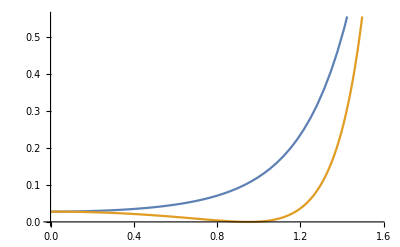

```mathematica
Plot[{ReflectedPowerS[1,1.4,θ],ReflectedPowerP[1,1.4,θ]},{θ,0,π/2}]
```

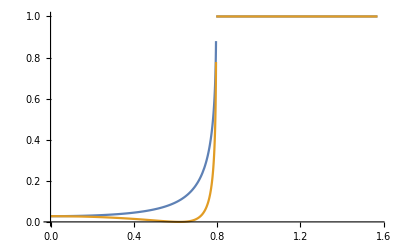

```mathematica
Plot[{ReflectedPowerS[1.4,1.,θ],ReflectedPowerP[1.4,1.,θ]},{θ,0,π/2}]
```

```mathematica
DipoleEmission[r_,θ_]:=3/(8 π)Sin[θ]^2/r^2
DipoleEmissionXY[x,y]:=x^2/((x^2+y^2)^2)HeavisideTheta[(x^2+y^2)^2-0.0001]
```

```mathematica
DipoleEmission[r,θ]ReflectedPowerP[1.4,1.,θ]
```

(3 Abs[(-1. Cos[θ]+1.4 √(1-1.96 Sin[θ]^2))/(1. Cos[θ]+1.4 √(1-1.96 Sin[θ]^2))]^2 Sin[θ]^2)/(8 π r^2)

```mathematica
2 NIntegrate[DipoleEmission[r,θ]ReflectedPowerP[1.4,1.,θ]2π r^2 Sin[θ]/.r->1,{θ,0,π/2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.797646}. NIntegrate obtained 0.442591 and 7.29503×10^-6 for the integral and error estimates.

0.885181

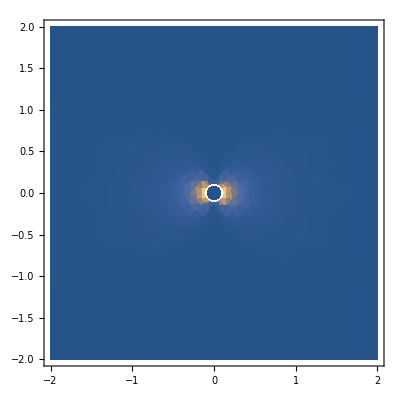

```mathematica
DensityPlot[DipoleEmissionXY[x,y],{x,-2,2},{y,-2,2},PlotRange->All]
```

```mathematica
CriticalAngle[n1_,n2_]:=ArcSin[n2/n1]
```

```mathematica
CriticalAngle[1.5,1.]
```

0.729728

```mathematica
TIR[θ_,n1_,n2_]:=HeavisideTheta[θ-CriticalAngle[n1,n2]]
```

```mathematica
2 Integrate[DipoleEmission[r,θ]TIR[θ,1.5,1]2π r^2 Sin[θ]/.r->1,{θ,0,π/2}]
```

0.910991